```mathematica
(*9.1*)
dataPCB={0.21,0.223,0.25,0.19,0.20,0.226,0.215,0.24,0.136};
dataNPCB={0.22,0.265,0.217,0.256,0.20,0.27,0.18,0.187,0.23};
gamma=Round[ (Variance[dataPCB]/Length[dataPCB]+Variance[dataNPCB]/Length[dataNPCB])^2/((Variance[dataPCB]/Length[dataPCB])^2/(Length[dataPCB]-1)+(Variance[dataNPCB]/Length[dataNPCB])^2/(Length[dataNPCB]-1))]
T = ((Mean[dataPCB] - Mean[dataNPCB])-(0))/Sqrt[Variance[dataPCB]/Length[dataPCB]+Variance[dataNPCB]/Length[dataNPCB]]
t=InverseCDF[StudentTDistribution[gamma], 0.95]
TrueQ[T<-t]
```

16

-0.956149

1.74588

False

```mathematica
(*9.2 Paired T-test*)
dataD = {4,-4,37,15,-33,-9,48,46,-11,-15,-14,90,11,33,56};
T=N[Mean[dataD]/Sqrt[Variance[dataD]/15]]
InverseCDF[StudentTDistribution[14],0.95]
```

1.94587

1.76131

```mathematica
(*9.2 Wilcoxon signed rank test*)
data = {{161,"Visual"},{203,"Visual"},{235,"Visual"},{176,"Visual"},{201,"Visual"},{188,"Visual"},{228,"Visual"},{211,"Visual"},{191,"Visual"},{178,"Visual"},{159,"Visual"},{227,"Visual"},{193,"Visual"},{192,"Visual"},{212,"Visual"},{157,"Auditory"},{207,"Auditory"},{198,"Auditory"},{161,"Auditory"},{234,"Auditory"},{197,"Auditory"},{180,"Auditory"},{165,"Auditory"},{202,"Auditory"},{193,"Auditory"},{173,"Auditory"},{137,"Auditory"},{182,"Auditory"},{159,"Auditory"},{156,"Auditory"}};
Sort[data, #1[[1]]<#2[[1]]&]
w15 = 1+2+3+4.5+6.5+8+9+12+13+17.5+19+20+22+24+29
E15 = (15(15+15+1))/2
Var15 = (15*15(15+15+1))/(12 - (3^3+3)/12)
z = (190.5 - E15)/Sqrt[Var15]
1 - CDF[NormalDistribution[], z]
```

{{137,Auditory},{156,Auditory},{157,Auditory},{159,Auditory},{159,Visual},{161,Auditory},{161,Visual},{165,Auditory},{173,Auditory},{176,Visual},{178,Visual},{180,Auditory},{182,Auditory},{188,Visual},{191,Visual},{192,Visual},{193,Auditory},{193,Visual},{197,Auditory},{198,Auditory},{201,Visual},{202,Auditory},{203,Visual},{207,Auditory},{211,Visual},{212,Visual},{227,Visual},{228,Visual},{234,Auditory},{235,Visual}}

190.5

465/2

13950/19

-1.55003

0.939432

```mathematica
Grid[%35]
```

137 | Auditory
156 | Auditory
157 | Auditory
159 | Auditory
159 | Visual
161 | Auditory
161 | Visual
165 | Auditory
173 | Auditory
176 | Visual
178 | Visual
180 | Auditory
182 | Auditory
188 | Visual
191 | Visual
192 | Visual
193 | Auditory
193 | Visual
197 | Auditory
198 | Auditory
201 | Visual
202 | Auditory
203 | Visual
207 | Auditory
211 | Visual
212 | Visual
227 | Visual
228 | Visual
234 | Auditory
235 | Visual

```mathematica
(*9.3*)
k=(0*109+1*65+2*22+3*3+4*1)/200
f[i_]=N[(E^-k k^i)/(i!)]
f[0]
f[1]
f[2]
f[3]
1-Sum[f[i],{i, 0, 3}]
```

61/100

(0.543351 0.61^i)/(i!)

0.543351

0.331444

0.10109

0.0205551

0.00355962

```mathematica
200*f[0]
200*f[1]
200*f[2]
200*f[3]
200*(1-Sum[f[i],{i, 0, 3}])
```

108.67

66.2888

20.2181

4.11101

0.711924

```mathematica
200*f[0]
200*f[1]
200*f[2]
200*(1-Sum[f[i],{i, 0, 2}])
```

108.67

66.2888

20.2181

4.82293

```mathematica
f[0]
f[1]
1-Sum[f[i],{i, 0, 1}]
```

0.543351

0.331444

0.125205

```mathematica
X2=(109 - 108.67)^2/108.67+(65-66.29)^2/66.29+(26-25.04)^2/25.04
```

0.0629106

```mathematica
1-CDF[ChiSquareDistribution[1],0.063]
```

0.801816

{6.5,7.5,7.5,7.5,8,8,8.5,9.5,9.5,9.5,10,10.5,10.5,10.5,11,11,11,11.5,11.5,11.5,12,12,12,12.5,12.5,12.5,12.5,13,13,13,13,13,13.5,13.5,14,14,14,14,14,14,14,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,15,15,15,15,15,15.5,15.5,15.5,16,16,16,16,16.5,16.5,16.5,16.5,16.5,16.5,17,17,17,17,17,17,17,17,17,17,17,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,18,18,18,18,18,18.5,18.5,18.5,18.5,18.5,18.5,18.5,18.5,19,19,19,19,19,19,19.5,19.5,19.5,19.5,19.5,20,20,20,20,20,20,20,20.5,20.5,20.5,20.5,20.5,20.5,20.5,20.5,21,21,21,21,21,21,21,21.5,21.5,21.5,21.5,21.5,22,22,22,22,22,22,22,22.5,22.5,23.5,23.5,23.5,24,24,24,24,24,24,24.5,24.5,24.5,25,26,26.5}

165

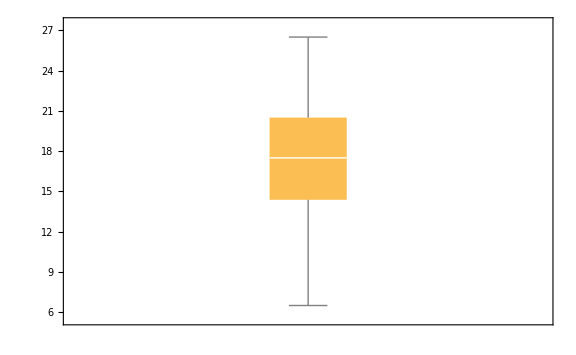

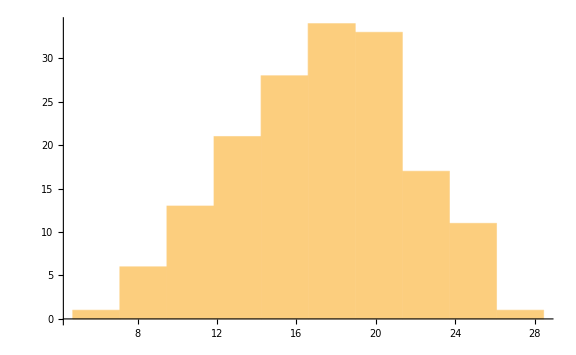

```mathematica
(*9.4 i*)
data = {
6.5,7.5,7.5,7.5,8,8,8.5,9.5,9.5,9.5,10,10.5,10.5,10.5,11,11,11,11.5,11.5,11.5,12,12,12,12.5,12.5,12.5,12.5,13,13,13,13,13,13.5,13.5,14,14,14,14,14,14,14,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,14.5,15,15,15,15,15,15.5,15.5,15.5,16,16,16,16,16.5,16.5,16.5,16.5,16.5,16.5,17,17,17,17,17,17,17,17,17,17,17,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,17.5,18,18,18,18,18,18.5,18.5,18.5,18.5,18.5,18.5,18.5,18.5,19,19,19,19,19,19,19.5,19.5,19.5,19.5,19.5,20,20,20,20,20,20,20,20.5,20.5,20.5,20.5,20.5,20.5,20.5,20.5,21,21,21,21,21,21,21,21.5,21.5,21.5,21.5,21.5,22,22,22,22,22,22,22,22.5,22.5,23.5,23.5,23.5,24,24,24,24,24,24,24.5,24.5,24.5,25,26,26.5
}
Length[data]
Needs["StatisticalPlots`"]
BoxWhiskerChart[data, ImageSize->Large]
Histogram[data, {"Raw", "FreedmanDiaconis"}, ImageSize -> Large]
```

```mathematica
(*9.4 ii*)
Mean[data]
Variance[data]
```

17.1576

18.8287

```mathematica
(*9.4 iii*)
Ceiling[2*Length[data]^(2/5)]
PearsonChiSquareTest[data, NormalDistribution[μ,σ], {"FittedDistributionParameters", "DegreesOfFreedom","TestDataTable"}]
```

16

{{μ→17.1576,σ→4.32603},13, | Statistic | P-Value
Pearson χ^2 | 30.9758 | 0.00339924}

```mathematica
(*9.5*)
O11=748;
O12=74;
O13=31;
O14=9;
O21=821;
O22=60;
O23=25;
O24=10;
O31=786;
O32=51;
O33=22;
O34=6;
O41=720;
O42=66;
O43=16;
O44=5;
O51=672;
O52=50;
O53=15;
O54=7;
n1=O11+O12+O13+O14
n2=O21+O22+O23+O24
n3=O31+O32+O33+O34
n4=O41+O42+O43+O44
n5=O51+O52+O53+O54
```

862

916

865

807

744

```mathematica
N1=O11+O21+O31+O41+O51
N2=O12+O22+O32+O42+O52
N3=O13+O23+O33+O43+O53
N4=O14+O24+O34+O44+O54
```

3747

301

109

37

```mathematica
n=n1+n2+n3+n4+n5
N1+N2+N3+N4
```

4194

4194

```mathematica
E11 = N[(n1 N1)/n]
E12 = N[(n1 N2)/n]
E13 =  N[(n1 N3)/n]
E14 =  N[(n1 N4)/n]
E21 =  N[(n2 N1)/n]
E22 =  N[(n2 N2)/n]
E23 = N[ (n2 N3)/n]
E24 = N[ (n2 N4)/n]
E31 = N[ (n3 N1)/n]
E32 = N[ (n3 N2)/n]
E33 = N[ (n3 N3)/n]
E34 = N[ (n3 N4)/n]
E41 = N[ (n4 N1)/n]
E42 = N[ (n4 N2)/n]
E43 = N[ (n4 N3)/n]
E44 = N[ (n4 N4)/n]
E51=  N[(n5 N1)/n]
E52 = N[ (n5 N2)/n]
E53 = N[ (n5 N3)/n]
E54 = N[ (n5 N4)/n]
```

770.127

61.865

22.403

7.60467

818.372

65.7406

23.8064

8.08107

772.808

62.0804

22.4809

7.63114

720.989

57.9177

20.9735

7.11946

664.704

53.3963

19.3362

6.56366

```mathematica
(O11-E11)^2/E11+(O12-E12)^2/E12+(O13-E13)^2/E13+(O14-E14)^2/E14+(O21-E21)^2/E21+(O22-E22)^2/E22+(O23-E23)^2/E23+(O24-E24)^2/E24+(O31-E31)^2/E31+(O32-E32)^2/E32+(O33-E33)^2/E33+(O34-E34)^2/E34+(O41-E41)^2/E41+(O42-E42)^2/E42+(O43-E43)^2/E43+(O44-E44)^2/E44+(O51-E51)^2/E51+(O52-E52)^2/E52+(O53-E53)^2/E53+(O54-E54)^2/E54
```

14.3953

```mathematica
InverseCDF[ChiSquareDistribution[12],0.95]
```

21.0261